## κ=1 (k=1/2), M=0

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
κ=1;
nmax=7;
```

```mathematica
(**)
(*
Subscript[Σ, N] z^N*Z(N)=Ξ(z)=Exp[1/2 Tr[Log[1+zρ]]]=Subscript[Σ, n] e^(J(μ+2πin)),
J=C/3 μ^3+Bμ+A+O(e^(-(...)μ))
*)
(**)
```

```mathematica
Clear[f];
CoefficientList[(Normal[Series[Exp[1/2*Sum[(-1)^(n-1)/n*z^n*f[n],{n,1,nmax}]],{z,0,nmax}]]//Expand),z]
```

{1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6,f[1]^4/384-1/32 f[1]^2 f[2]+f[2]^2/32+1/12 f[1] f[3]-f[4]/8,f[1]^5/3840-1/192 f[1]^3 f[2]+1/64 f[1] f[2]^2+1/48 f[1]^2 f[3]-1/24 f[2] f[3]-1/16 f[1] f[4]+f[5]/10,f[1]^6/46080-(f[1]^4 f[2])/1536+1/256 f[1]^2 f[2]^2-f[2]^3/384+1/288 f[1]^3 f[3]-1/48 f[1] f[2] f[3]+f[3]^2/72-1/64 f[1]^2 f[4]+1/32 f[2] f[4]+1/20 f[1] f[5]-f[6]/12,f[1]^7/645120-(f[1]^5 f[2])/15360+(f[1]^3 f[2]^2)/1536-1/768 f[1] f[2]^3+(f[1]^4 f[3])/2304-1/192 f[1]^2 f[2] f[3]+1/192 f[2]^2 f[3]+1/144 f[1] f[3]^2-1/384 f[1]^3 f[4]+1/64 f[1] f[2] f[4]-1/48 f[3] f[4]+1/80 f[1]^2 f[5]-1/40 f[2] f[5]-1/24 f[1] f[6]+f[7]/14}

```mathematica
Table[(
f[n]=Import[StringJoin["kappa1/210220_trrho_kappa1_n",ToString[n],".m"]]//FullSimplify//Expand;
Print["n=",n,"    ",f[n]];
),{n,1,nmax}];
```

n=1    1/(24 π^2)

n=2    1/(1920 π^6)+1/(1152 π^4)-1/(75600 π^2)

n=3    -1/(286720 π^8)+11/(2764800 π^6)+2311/(116121600 π^4)-1763/(931392000 π^2)

n=4    13/(189235200 π^12)+1/(3686400 π^10)+1/(16257024000 π^8)-14893/(73156608000 π^6)+306161/(1005903360000 π^4)-33161/(1165404240000 π^2)

n=5    -41/(55105290240 π^14)-137/(163499212800 π^12)+2293/(312134860800 π^10)+5066227/(1081547292672000 π^8)-5418197/(860823355392000 π^6)+21172303/(5370182737920000 π^4)-100577927/(295960839779404800 π^2)

n=6    3373/(374715973632000 π^18)+4871/(88168464384000 π^16)+24491/(495947612160000 π^14)-916747/(9613753712640000 π^12)+1536779/(27038682316800000 π^10)+183202252943/(1113561092535091200000 π^8)-62646855212069/(538337190672433152000000 π^6)+122970074687/(2630763020261376000000 π^4)-7167457201/(1928678139229121280000 π^2)

n=7    -1709/(12517984174080000 π^20)-98027/(231253286584320000 π^18)+3785389/(2856658246041600000 π^16)+121358023/(35351145794764800000 π^14)-276011347/(163159134437376000000 π^12)-296531819027/(200440996656316416000000 π^10)+518198019451579/(143872093155533783040000000 π^8)-459412350324479/(263016170299960197120000000 π^6)+577375090738104409/(1099809422114014118707200000000 π^4)-255567041/(6581122140389981184000 π^2)

```mathematica
zZN={1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6,f[1]^4/384-1/32 f[1]^2 f[2]+f[2]^2/32+1/12 f[1] f[3]-f[4]/8,f[1]^5/3840-1/192 f[1]^3 f[2]+1/64 f[1] f[2]^2+1/48 f[1]^2 f[3]-1/24 f[2] f[3]-1/16 f[1] f[4]+f[5]/10,f[1]^6/46080-(f[1]^4 f[2])/1536+1/256 f[1]^2 f[2]^2-f[2]^3/384+1/288 f[1]^3 f[3]-1/48 f[1] f[2] f[3]+f[3]^2/72-1/64 f[1]^2 f[4]+1/32 f[2] f[4]+1/20 f[1] f[5]-f[6]/12,f[1]^7/645120-(f[1]^5 f[2])/15360+(f[1]^3 f[2]^2)/1536-1/768 f[1] f[2]^3+(f[1]^4 f[3])/2304-1/192 f[1]^2 f[2] f[3]+1/192 f[2]^2 f[3]+1/144 f[1] f[3]^2-1/384 f[1]^3 f[4]+1/64 f[1] f[2] f[4]-1/48 f[3] f[4]+1/80 f[1]^2 f[5]-1/40 f[2] f[5]-1/24 f[1] f[6]+f[7]/14};
zZNlist=Table[{i-1,zZN[[i]]},{i,1,nmax+1}];
```

```mathematica
zZN[[1+1]]//Expand
zZN[[2+1]]//Expand
zZN[[3+1]]//Expand
zZN[[4+1]]//Expand
zZN[[5+1]]//Expand
zZN[[6+1]]//Expand
zZN[[7+1]]//Expand
```

1/(48 π^2)

-1/(7680 π^6)+1/(302400 π^2)

-17/(5160960 π^8)-13/(5529600 π^6)+337/(99532800 π^4)-1763/(5588352000 π^2)

-1/(9083289600 π^12)-19/(412876800 π^10)-151/(65028096000 π^8)+110671/(1170505728000 π^6)-10879/(243855360000 π^4)+33161/(9323233920000 π^2)

-1/(991895224320 π^14)-1583/(3269984256000 π^12)+731/(1498247331840 π^10)+348757/(337983528960000 π^8)-17004137/(12051526975488000 π^6)+225860389/(483316446412800000 π^4)-100577927/(2959608397794048000 π^2)

23/(323754601218048000 π^18)+89/(12696258871296000 π^16)-606803/(142832912302080000 π^14)+273731/(30764011880448000 π^12)+11111333/(3460951336550400000 π^10)-369357430831/(17816977480561459200000 π^8)+215989200687971/(12920092576138395648000000 π^6)-814993194619/(179445730224144384000000 π^4)+7167457201/(23144137670749455360000 π^2)

4973/(2952641963108597760000 π^20)+3277/(17266912064962560000 π^18)-91615637/(2879511512009932800000 π^16)+1570580677/(15837313316054630400000 π^14)-273553817/(4399253698904064000000 π^12)-14535520549283/(89797566502029754368000000 π^10)+4084729947556969/(13862499328750843330560000000 π^8)-661077767954033/(3682226384199442759680000000 π^6)+9532006332801721/(223149737820234748723200000000 π^4)-255567041/(92135709965459736576000 π^2)

```mathematica
N[zZNlist,3]//MatrixForm
```

(0 | 1.
1. | 0.00211
2. | 2.×10^-7
3. | 1.63×10^-12
4. | 1.73×10^-18
5. | 3.05×10^-25
6. | 1.09×10^-32
7. | 8.9×10^-41)

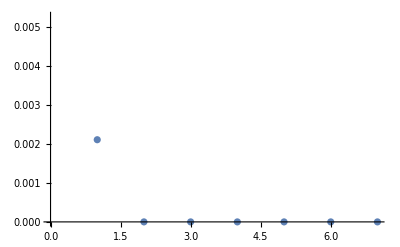

```mathematica
ListPlot[zZNlist]
```

```mathematica
k=κ/2;
```

```mathematica
(*airy:*)
aABJM[kk_]:=If[EvenQ[kk],
-Zeta[3]/(π^2*kk)-2/kk*Sum[m*(kk/2-m)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk/2-1}],
-Zeta[3]/(8*π^2*kk)+kk/4*Log[2]-1/kk*Sum[(kk+(-1)^m*(2*m-kk))/4*(kk-(kk+(-1)^m*(2*m-kk))/4)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk-1}]
];
aA=1/2*(aABJM[8*k]+16*aABJM[4*k]);
cC=3/(32*π^2*k);
bB=(π^2*cC)/3-3/(16*k)+k/2;
logZpert=Table[{nN,Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)]},{nN,0,8,0.01}];
```

```mathematica
range={{0,8},All};
imsize=400;
plot1=ListLogPlot[{zZNlist,logZpert,zZNlist},Joined->{False,True,False},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[1]]},PlotMarkers->{{"●",10},"",{"●",10}},PlotRange->range,Frame->True,FrameLabel->{"N","Z_(1/2, 0)(N)"},PlotLegends->Placed[{"Z_(1/2, 0)(N)","e^AC^(-1/3)Ai[C^(-1/3)(N-B)]"},{0.75,0.8}],ImageSize->imsize]
```

-Graphics-

```mathematica
deviations=Table[{√nN,Abs[zZN[[nN+1]]/(Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)])-1]},{nN,0,nmax}];
```

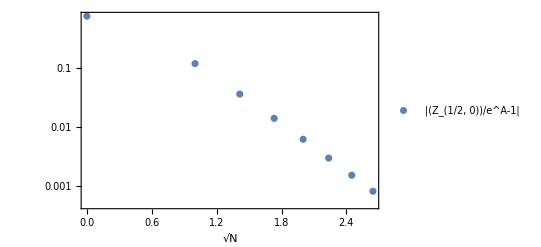

```mathematica
range=All;
origin=Automatic;
(*
range={{0,8},All};
*)
imsize=400;
(*
origin={0,0};
*)
plot2=ListLogPlot[deviations,AxesOrigin->origin,Frame->True,FrameLabel->{"√N",""},ImageSize->imsize,PlotLegends->Placed[{"|(Z_(1/2, 0))/e^A-1|"},{0.75,0.8}]]
```

```mathematica
Row[{plot1,plot2}]
```

-Graphics--Graphics-

```mathematica
Export["210220_affineD4_Z_vs_Airy_kappa1_M0.pdf",Style[%,LineBreakWithin->False]];
```

## κ=2 (k=1), M=0

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
κ=2;
nmax=4;
```

```mathematica
(**)
(*
Subscript[Σ, N] z^N*Z(N)=Ξ(z)=Exp[1/2 Tr[Log[1+zρ]]]=Subscript[Σ, n] e^(J(μ+2πin)),
J=C/3 μ^3+Bμ+A+O(e^(-(...)μ))
*)
(**)
```

```mathematica
Clear[f];
CoefficientList[(Normal[Series[Exp[1/2*Sum[(-1)^(n-1)/n*z^n*f[n],{n,1,nmax}]],{z,0,nmax}]]//Expand),z]
```

{1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6,f[1]^4/384-1/32 f[1]^2 f[2]+f[2]^2/32+1/12 f[1] f[3]-f[4]/8}

```mathematica
Table[(
f[n]=Import[StringJoin["kappa2/210220_trrho_kappa2_n",ToString[n],".m"]]//FullSimplify//Expand;
Print["n=",n,"    ",f[n]];
),{n,1,nmax}];
```

n=1    1/(48 π^2)

n=2    -3/262144+1/(61440 π^6)+25/(147456 π^4)+36277/(309657600 π^2)

n=3    -21/134217728-1/(36700160 π^8)-323/(2831155200 π^6)+627211/(237817036800 π^4)+158789857/(122079412224000 π^2)

n=4    -477/274877906944+13/(387553689600 π^12)+229/(211392921600 π^10)+3451081/(532710162432000 π^8)-17763713/(4794391461888000 π^6)+12883349449/(602723498065920000 π^4)+14092460051237/(938507455766200320000 π^2)

```mathematica
zZN={1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6,f[1]^4/384-1/32 f[1]^2 f[2]+f[2]^2/32+1/12 f[1] f[3]-f[4]/8};
zZNlist=Table[{i-1,zZN[[i]]},{i,1,nmax+1}];
```

```mathematica
zZN[[1+1]]//Expand
zZN[[2+1]]//Expand
zZN[[3+1]]//Expand
zZN[[4+1]]//Expand
```

1/(96 π^2)

3/1048576-1/(245760 π^6)+7/(589824 π^4)-36277/(1238630400 π^2)

-7/268435456-31/(660602880 π^8)-1541/(5662310400 π^6)+191887/(1426902220800 π^4)+180619357/(732476473344000 π^2)

243/1099511627776+19/(4650644275200 π^12)-293/(1268357529600 π^10)-3834259/(2130840649728000 π^8)+59868161/(12785043898368000 π^6)+828980993/(16876257945845760000 π^4)-8380522497631/(3754029823064801280000 π^2)

```mathematica
N[zZNlist,3]//MatrixForm
```

(0 | 1.
1. | 0.00106
2. | 1.11×10^-8
3. | 2.72×10^-15
4. | 3.02×10^-23)

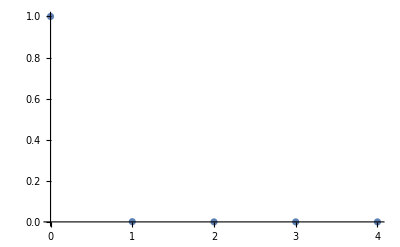

```mathematica
ListPlot[zZNlist]
```

```mathematica
k=κ/2;
```

```mathematica
(*airy:*)
aABJM[kk_]:=If[EvenQ[kk],
-Zeta[3]/(π^2*kk)-2/kk*Sum[m*(kk/2-m)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk/2-1}],
-Zeta[3]/(8*π^2*kk)+kk/4*Log[2]-1/kk*Sum[(kk+(-1)^m*(2*m-kk))/4*(kk-(kk+(-1)^m*(2*m-kk))/4)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk-1}]
];
aA=1/2*(aABJM[8*k]+16*aABJM[4*k]);
cC=3/(32*π^2*k);
bB=(π^2*cC)/3-3/(16*k)+k/2;
logZpert=Table[{nN,Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)]},{nN,0,nmax+1,0.01}];
```

```mathematica
range={{0,nmax+1},All};
imsize=400;
plot1=ListLogPlot[{zZNlist,logZpert,zZNlist},Joined->{False,True,False},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[1]]},PlotMarkers->{{"●",10},"",{"●",10}},PlotRange->range,Frame->True,FrameLabel->{"N","Z_(1, 0)(N)"},PlotLegends->Placed[{"Z_(1, 0)(N)","e^AC^(-1/3)Ai[C^(-1/3)(N-B)]"},{0.75,0.8}],ImageSize->imsize]
```

-Graphics-

```mathematica
deviations=Table[{√nN,Abs[zZN[[nN+1]]/(Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)])-1]},{nN,0,nmax}];
```

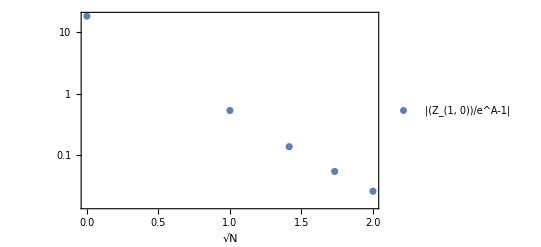

```mathematica
range=All;
origin=Automatic;
(*
range={{0,8},All};
*)
imsize=400;
(*
origin={0,0};
*)
plot2=ListLogPlot[deviations,AxesOrigin->origin,Frame->True,FrameLabel->{"√N",""},ImageSize->imsize,PlotLegends->Placed[{"|(Z_(1, 0))/e^A-1|"},{0.75,0.8}]]
```

```mathematica
Row[{plot1,plot2}]
```

-Graphics--Graphics-

```mathematica
Export["210220_affineD4_Z_vs_Airy_kappa2_M0.pdf",Style[%,LineBreakWithin->False]];
```